```mathematica
segWidth = 0.1;
segLength = 0.5;
xTotal = 0;
zTotal = 0;
totalAngle = 0;
servos = {0.0,Pi/8, 0.0, -Pi/8, 0.0};

nextSeg[xTotal_,zTotal_,totalAngle_, nextServo_] := Module[{newXTotal,newZTotal,tempAngle},
tempAngle = totalAngle;
newXTotal=xTotal+segLength*Cos[tempAngle];newZTotal=zTotal+segLength*Sin[tempAngle];
tempAngle=totalAngle+nextServo;
{newXTotal,newZTotal, tempAngle}
];

listSegs[initX_,initY_,initAngle_, servos_] := Module[{results},

results = NestList[( ind = #[[4]];  result =nextSeg[ #[[1]], #[[2]], #[[3]],servos[[ind]]];  Append[result,ind + 1])&,{initX,initY,initAngle,1},Length[servos]];

results
];


getSeg[xTotal_, zTotal_, totalAngle_] := Module[{p1,p2,p3,p4},

p1 = {xTotal-0.5*segWidth*Sin[totalAngle],zTotal+0.5*segWidth*Cos[totalAngle]};
p2={xTotal+0.5*segWidth*Sin[totalAngle],zTotal-0.5*segWidth*Cos[totalAngle]};		p3={xTotal+segLength*Cos[totalAngle]+0.5*segWidth*Sin[totalAngle],zTotal+segLength*Sin[totalAngle]-0.5*segWidth*Cos[totalAngle]};p4={xTotal+segLength*Cos[totalAngle]-0.5*segWidth*Sin[totalAngle],zTotal+segLength*Sin[totalAngle]+0.5*segWidth*Cos[totalAngle]};

Polygon[{p4,p3,p2,p1}]
];
```

```mathematica
(* iterative execution of indexing the servo array *)
Array[(result = nextSeg[0,0,0,servos[[#]]]; )&,4];
```

```mathematica
(* demonstration of using the NestedList to recursively compute the segment positions *)
NestList[( ind = #[[4]];  result =nextSeg[ #[[1]], #[[2]], #[[3]],servos[[ind]]];  Append[result,ind + 1])&,{0,0,0,1},4];
```

```mathematica
(* Plot the robot given joint configuration in servos *)
buildSnake[A1_,numSegs_]:= Module[{servos,results},
(*servos = {A1,A1, A1, A1, A1}; *)
servos = Table[A1,{numSegs}];
(*servos = {A1,Pi/8, 0.0, -Pi/8, 0.0};*)
results =listSegs[0,0,0,servos];
Map[{EdgeForm[{Thick,Black}],FaceForm[Blue], Opacity[0.4],getSeg[#[[1]],#[[2]],#[[3]]]}&,results] 
];

Manipulate[Graphics[buildSnake[T1,segs],PlotRange->{{0,2},{-0.7,0.7}}],{{T1,0},-Pi/2,Pi/2}, {segs,0,20}]
```

```mathematica
(* Plot the robot given joint configuration in servos *)
buildSineSnake[freq_,numSegs_]:= Module[{servos,results},
servos = Table[Sin[freq*x/10],{x,1,numSegs}];
results =listSegs[0,0,0,servos];
Map[{EdgeForm[{Thick,Black}],FaceForm[Blue], Opacity[0.4],getSeg[#[[1]],#[[2]],#[[3]]]}&,results] 
];

Manipulate[Graphics[buildSineSnake[T1,segs],PlotRange->{{0,2},{-0.7,0.7}}],{{T1,0},0,4Pi}, {segs,1,20}]
```

y==Cos[(π x)/2]

1==x^2+(-1/2+y)^2

{x→0.924374,y→0.118513}

{x→-0.924374,y→0.118513}

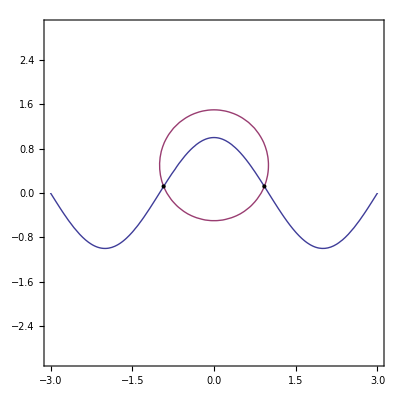

0.363759

```mathematica
(* Solving for intersections with a guessed solution *)
date1=DateList[];
expr1 = y ==(1)Cos[(2Pi/4)x]
expr2 = 1== (x/1)^2+((y-1/2)/1)^2
rts = Reduce[Evaluate[expr1] && Evaluate[expr2] &&2>x > -2 &&  0< y < 3,{x,y}, Reals];

rule1 = FindRoot[Evaluate[expr1] && Evaluate[expr2],{x,0.5},{y,0.5}]
rule2 = FindRoot[Evaluate[expr1] && Evaluate[expr2],{x,-0.5},{y,0.5}]

points = Point[{x,y}] /. {rule1,rule2};

ContourPlot[Evaluate[{expr1,expr2}],{x,-3,3},{y,-3,3},Epilog->{PointSize[Medium],points}]

(*Determine number of seconds passed *)
date2 = DateList[];
date2[[6]]-date1[[6]]
```

```mathematica
{x->0.9243743357234963,y->0.11851331942550727}
```

{x→0.924374,y→0.118513}

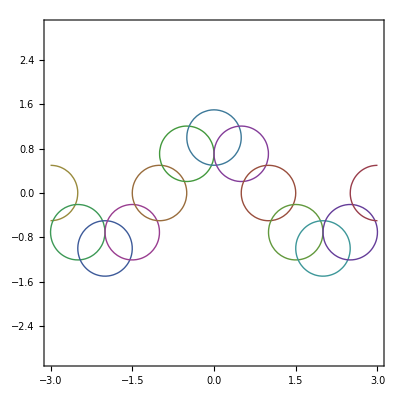

```mathematica
expr1 = y ==(1)Cos[(2Pi/4)x];

fitSolutions[pnt_] :=Module[{guessX1,guessX2,guessY1,guessY2,circExpr,intersections},

guessX1= pnt[[1]] + segWidth;
guessX2= pnt[[1]] - segWidth;
guessY1 = pnt[[2]];
guessY2 = pnt[[2]];

circExpr =((segLength)^2 == (x-pnt[[1]])^2 + (y-pnt[[2]])^2);

intersections ={FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,guessX1},{y,guessY2}],
FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,guessX2},{y,guessY2}]};


{circExpr,{x,y} /.intersections}

];


Clear[makeCircle]
makeCircle[pnt_] :=Module[{kjkj},
((segLength)^2 == (x-pnt[[1]])^2 + (y-pnt[[2]])^2)
];

(* sample points on a curve *)
pnts = Table[{x, y /.Solve[expr1,y][[1]]},{x,-4,4,0.5}];

Map[fitSolutions,pnts];

(* create circles centered on each point *)
circles = Evaluate[Map[makeCircle,pnts]];

Clear[getRules]
getRules[circExpr_] := Module[{dfdd},
{FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,4},{y,0}],
FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,-4},{y,0}]}
];

(*
Map[getRules,circles];
*)
ContourPlot[Evaluate[circles], {x,-3,3},{y,-3,3}]

(*
circles = Table[1 == (x-#1)^2 + (y-#2)^2 &, pnts]
*)
expr2 =((segLength)^2 == (x-1)^2 + (y-1)^2);



(*
rts = Reduce[Evaluate[expr1] && Evaluate[expr2] &&2>x > -2 &&  0< y < 3,{x,y}, Reals];
*)

(*
rule1 = FindRoot[Evaluate[expr1] && Evaluate[expr2],{x,0.5},{y,0.5}];
rule2 = FindRoot[Evaluate[expr1] && Evaluate[expr2],{x,-0.5},{y,0.5}];

points = Point[{x,y}] /. {rule1,rule2};

ContourPlot[Evaluate[{expr1,circles}],{x,-3,3},{y,-3,3},Epilog->{PointSize[Medium],points}];
*)
```

```mathematica
plotCircles[a_,f_] := Module[{fdafdf},

expr1 = y ==(a)Cos[(f/4)x];

(*expr1 = y ==(1)Cos[(2Pi/4)x];*)

fitSolutions[pnt_] :=Module[{guessX1,guessX2,guessY1,guessY2,circExpr,intersections},

guessX1= pnt[[1]] + segLength;
guessX2= pnt[[1]] - segLength;
guessY1 = pnt[[2]];
guessY2 = pnt[[2]];

circExpr =((segLength)^2 == (x-pnt[[1]])^2 + (y-pnt[[2]])^2);

intersections ={FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,guessX1},{y,guessY2}],
FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,guessX2},{y,guessY2}]};

(*{circExpr,{x,y} /.intersections}*)

{circExpr,intersections}

];

(* sample points on a curve *)
samplePoints = Table[{x, y /.Solve[expr1,y][[1]]},{x,0,6,0.3}];

results = Map[fitSolutions,samplePoints];
transResults = Transpose[results];
circles = transResults[[1]];
points = transResults[[2]];

graphPoints = Point[{x,y}] /.  points;

ContourPlot[Evaluate[{expr1,circles}], {x,0,6},{y,-3,3},Epilog->{PointSize[Medium],graphPoints}]
]

Manipulate[plotCircles[a,f],{{a,1},0,2},{{f,2Pi},Pi/8,4Pi}]
```

```mathematica
Clear[plotFitCurve]
Clear[fitSolutions]
plotFitCurve[a_,f_] := Module[{fdafdf},

expr1 = y ==(a)Cos[(f/4)x];

fitSolutions[pnt_] :=Module[{guessX1,guessX2,guessY1,guessY2,circExpr,intersections,highInter},

guessX1= pnt[[1]] + segLength;
guessX2= pnt[[1]] - segLength;
guessY1 = pnt[[2]];
guessY2 = pnt[[2]];

circExpr =((segLength)^2 == (x-pnt[[1]])^2 + (y-pnt[[2]])^2);

intersections ={FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,guessX1},{y,guessY2}],
FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,guessX2},{y,guessY2}]};

highInter = If[(x /. intersections[[1]]) > (x/.intersections[[2]]) , intersections[[1]],intersections[[2]]];

{circExpr,highInter, {x,y} /.highInter}

];

currResult = {(segLength^2 == x^2 + (y-a)^2),{x->0,y->a},{0,a}};
totalResults = {currResult};
While[currResult[[3]][[1]] <4,currResult = fitSolutions[currResult[[3]]];totalResults = Append[totalResults,currResult];];

transResults = Transpose[totalResults];
circles = transResults[[1]];

points = transResults[[2]];

graphPoints = Point[{x,y}] /.  points;

ContourPlot[Evaluate[{expr1,circles}], {x,0,6},{y,-3,3},Epilog->{PointSize[Medium],graphPoints}]


]

(*plotFitCurve[1,2Pi]*)
Manipulate[plotFitCurve[a,f],{{a,1},0,2},{{f,2Pi},Pi/8,4Pi}]
```

```mathematica
Clear[plotFitSegments]
plotFitSegments[a_,f_,segLength_,segWidth_] := Module[{expr1},

expr1 = y ==(a)Cos[(f/4)x];

renderSeg[xTotal_, zTotal_, totalAngle_,segLen_,segWid_] := Module[{p1,p2,p3,p4},

p1 = {xTotal-0.5*segWid*Sin[totalAngle],zTotal+0.5*segWid*Cos[totalAngle]};
p2={xTotal+0.5*segWid*Sin[totalAngle],zTotal-0.5*segWid*Cos[totalAngle]};		p3={xTotal+segLen*Cos[totalAngle]+0.5*segWid*Sin[totalAngle],zTotal+segLen*Sin[totalAngle]-0.5*segWid*Cos[totalAngle]};p4={xTotal+segLen*Cos[totalAngle]-0.5*segWid*Sin[totalAngle],zTotal+segLen*Sin[totalAngle]+0.5*segWid*Cos[totalAngle]};

Polygon[{p4,p3,p2,p1}]

];

buildSnakeFromPoses[poses_]:= Module[{servos,results},
Map[{EdgeForm[{Thick,Black}],FaceForm[Blue], Opacity[0.4],renderSeg[#[[1]],#[[2]],#[[3]],segLength,segWidth]}&,poses] 
];

fitSolutions[pnt_] :=Module[{guessX1,guessX2,guessY1,guessY2,circExpr,intersections,highInter},

guessX1= pnt[[1]] + segLength;
guessX2= pnt[[1]] - segLength;
guessY1 = pnt[[2]];
guessY2 = pnt[[2]];

circExpr =((segLength)^2 == (x-pnt[[1]])^2 + (y-pnt[[2]])^2);

intersections ={FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,guessX1},{y,guessY2}],
FindRoot[Evaluate[expr1] && Evaluate[circExpr],{x,guessX2},{y,guessY2}]};

highInter = If[(x /. intersections[[1]]) > (x/.intersections[[2]]) , intersections[[1]],intersections[[2]]];

{circExpr,highInter, {x,y} /.highInter}

];

currResult = {(segLength^2 == x^2 + (y-a)^2),{x->0,y->a},{0,a}};
totalResults = {currResult};
While[currResult[[3]][[1]] <4,
currResult = fitSolutions[currResult[[3]]];totalResults = Append[totalResults,currResult];
];

For[i=1,i<Length[totalResults],i++,

pnt1 = totalResults[[i]][[3]];
pnt2 = totalResults[[i+1]][[3]];
dist = Sqrt[(pnt2[[1]]-pnt1[[1]])^2 + (pnt2[[2]]-pnt1[[2]])^2];

angle = ArcTan[(pnt2[[2]]-pnt1[[2]])/(pnt2[[1]]-pnt1[[1]])];

totalResults[[i]][[3]] = Append[totalResults[[i]][[3]],angle];
];

(* drop off the last element *)
totalResults =Delete[totalResults,-1];

transResults = Transpose[totalResults];

poses = transResults[[3]];

buildSnakeFromPoses[poses];


ContourPlot[Evaluate[{expr1}], {x,0,6},{y,-3,3},Epilog->buildSnakeFromPoses[poses]]

(*ContourPlot[Evaluate[{expr1}], {x,0,6},{y,-3,3}]*)

(*
ContourPlot[Evaluate[[expr1]], {x,0,6},{y,-3,3},Epilog->buildSnakeFromPoses[poses]]
*)

(*
Graphics[buildSnakeFromPoses[poses]]
*)

(*
circles = transResults[[1]];

points = transResults[[2]];

graphPoints = Point[{x,y}] /.  points;

(*
Manipulate[Graphics[buildSnakeFromPoses[T1,segs],PlotRange->{{0,2},{-0.7,0.7}}],{{T1,0},0,4Pi}, {segs,1,20}
*)

ContourPlot[Evaluate[{expr1,circles}], {x,0,6},{y,-3,3},Epilog->{PointSize[Medium],graphPoints}]
*)

]

(*plotFitSegments[1,2Pi]*)
Manipulate[plotFitSegments[a,f,sl,sw],{{a,1,"Amplitude"},0,2},{{f,2Pi,"Frequency"},Pi/8,4Pi},{{sl,0.5,"Segment Length"},0.05,0.3},{{sw,0.1,"Segment Width"},0.02,0.3}]
```

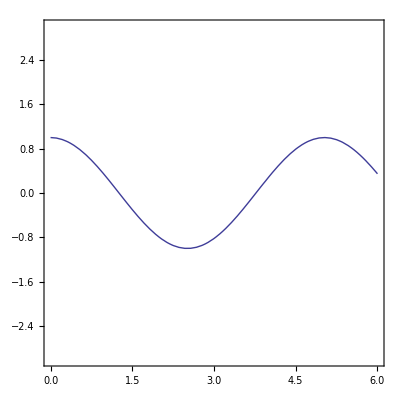

```mathematica
f = 5;
a = 1;
expr1 = y ==(a)Cos[(f/4)x];
ContourPlot[Evaluate[{expr1}], {x,0,6},{y,-3,3}]
```